### Controller Design

```mathematica
Cc=Kp + Ki/s; P=A/(1+τ s);
```

```mathematica
T=(Cc P)/(1 + Cc P)//FullSimplify
```

(1+s)/(1+s (2+s τ))

```mathematica
A=1; Ki = 1; Kp =1;τ=1;
```

```mathematica
Plot[Simplify[OutputResponse[P,UnitStep[t],t]],{t,0,10}]
```

-Graphics-

{ⅇ^-t (-1+ⅇ^t-t) UnitStep[t]+ⅇ^-t t UnitStep[t]}

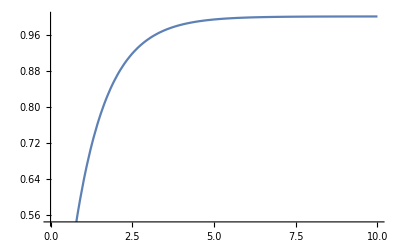

```mathematica
OutputResponse[(1+s)/(1+s (2+s ))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,UnitStep[t],t]
Plot[%,{t,0,10}]
```